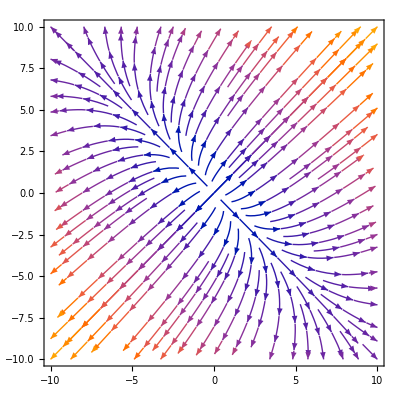

```mathematica
StreamPlot[{5/4x + 3/4y, 3/4x+5/4y},{x,-10,10},{y,-10,10}]
```

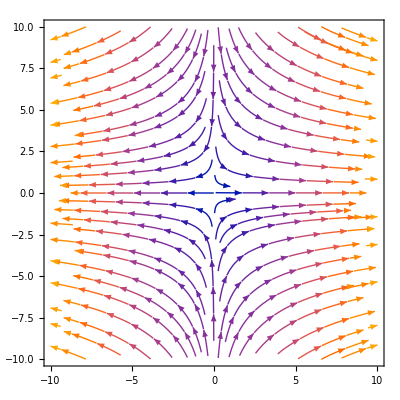

```mathematica
StreamPlot[{3x, -y},{x,-10,10},{y,-10,10}]
```

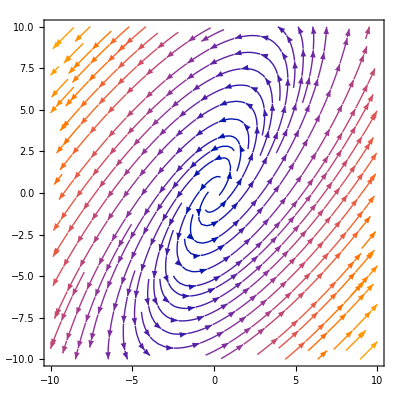

```mathematica
StreamPlot[{3x-2y, 4x-y},{x,-10,10},{y,-10,10}]
```

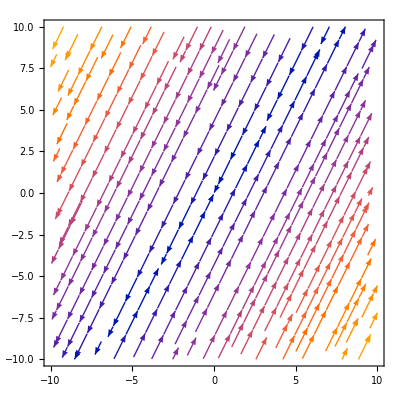

```mathematica
StreamPlot[{4x-3y, 8x-6y},{x,-10,10},{y,-10,10}]
```

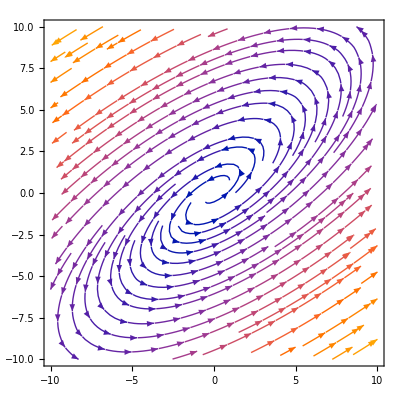

```mathematica
StreamPlot[{2x-5/2y, 9/5x-1y},{x,-10,10},{y,-10,10}]
```

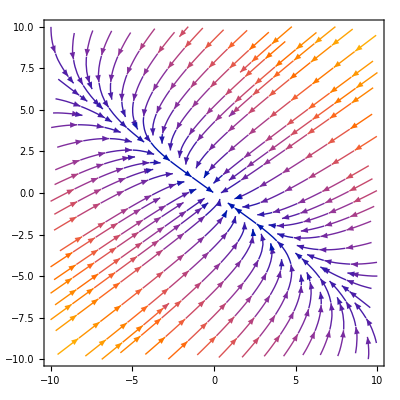

```mathematica
StreamPlot[{-x-y,-0.5x-y},{x,-10,10},{y,-10,10}]
```

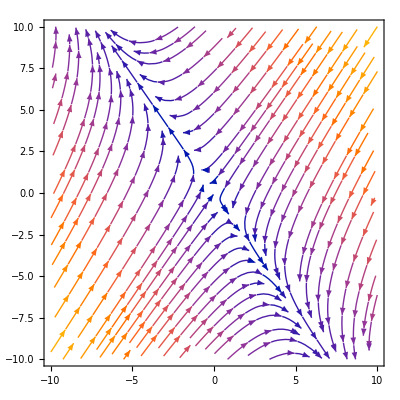

```mathematica
StreamPlot[{-x-y,-2x-y},{x,-10,10},{y,-10,10}]
```

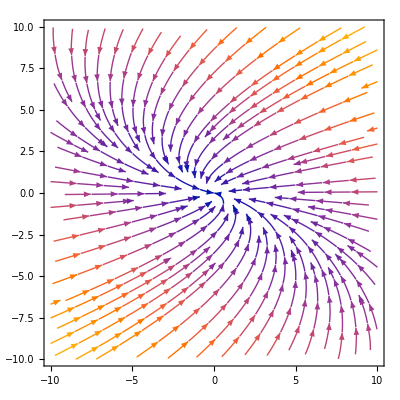

```mathematica
StreamPlot[{-x-y,-y},{x,-10,10},{y,-10,10}]
```

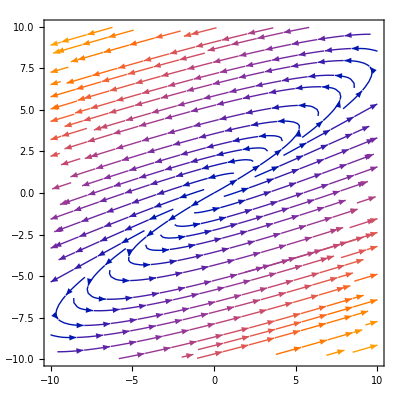

```mathematica
StreamPlot[{3x-4y,x-y},{x,-10,10},{y,-10,10}]
```

```mathematica
StreamPlot[{4x-2y,8x-4y},{x,-10,10},{y,-10,10}]
```

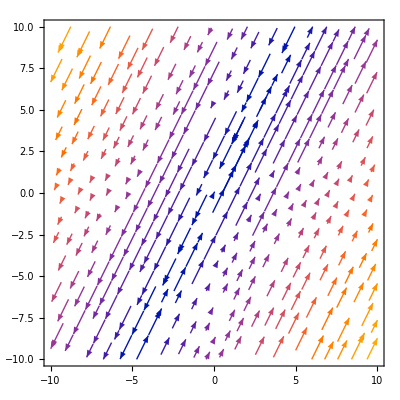

-Graphics-

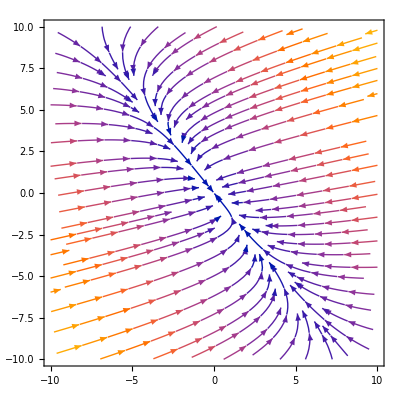

```mathematica
StreamPlot[{-3/2x-y,-1/4x-1/2y},{x,-10,10},{y,-10,10}]
```

```mathematica
VectorPlot3D[{x+y+z,2x+y-z,-y+z},{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
StreamPlot[{3x-4y,x-y},{x,-10,10},{y,-10,10}]
```

-Graphics-

```mathematica
StreamPlot[{3x-4y,x-y},{x,-10,10},{y,-10,10}], ContourPlot[{3x-4y==0,x-y==0},{x,-10,10},{y,-10,10}]
```

Syntax::tsntxi: "StreamPlot[{3x-4y,x-y},{x,-10,10},{y,-10,10}],ContourPlot[{3x-4y==0,x-y==0},{x,-10,10},{y,-10,10}]" is incomplete; more input is needed.

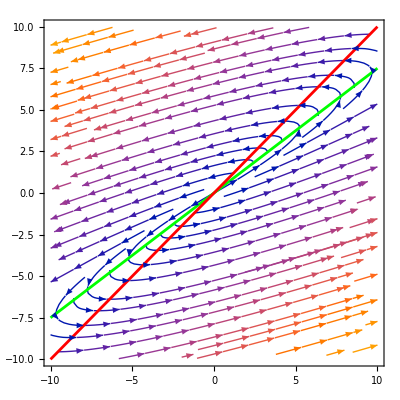

```mathematica
Show[StreamPlot[{3 x-4 y,x-y},{x,-10,10},{y,-10,10},StreamStyle->Arrowheads[0.02]],ContourPlot[{3 x-4 y==0,x-y==0},{x,-10,10},{y,-10,10},ContourStyle->{Green,Red}]]
```

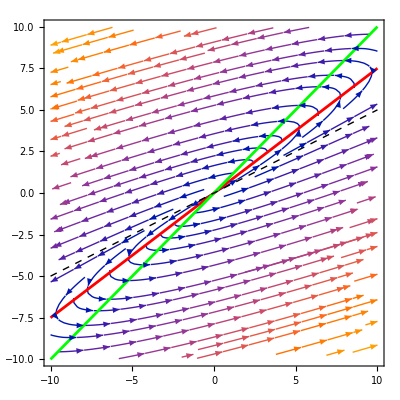

```mathematica
Show[(*1. The Vector Field*)StreamPlot[{3 x-4 y,x-y},{x,-10,10},{y,-10,10}],(*2. The Nullclines*)ContourPlot[{3 x-4 y==0,x-y==0},{x,-10,10},{y,-10,10},ContourStyle->{Red,Green}],(*3. The Eigendirection*)Plot[0.5 x,{x,-10,10},PlotStyle->{Black,Dashed,Thick}]]
```

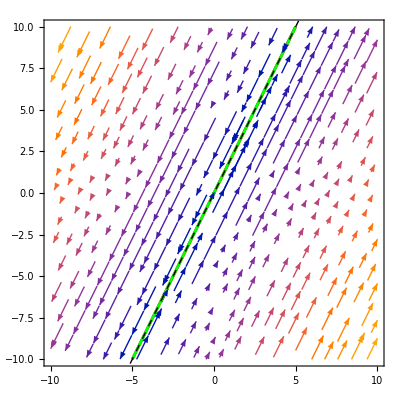

```mathematica
Show[(*1. The Vector Field*)StreamPlot[{4 x-2 y,8x-4y},{x,-10,10},{y,-10,10}],(*2. The Nullclines*)ContourPlot[{4 x-2 y==0,8x-4y==0},{x,-10,10},{y,-10,10},ContourStyle->{Red,Green}],(*3. The Eigendirection*)Plot[2 x,{x,-10,10},PlotStyle->{Black,Dashed,Thick}]]
```

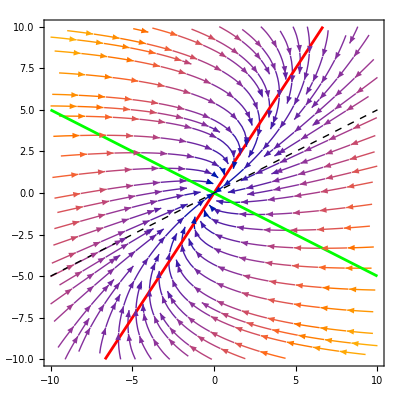

```mathematica
Show[(*1. The Vector Field*)StreamPlot[{-3/2x+1 y,-1/4x-1/2y},{x,-10,10},{y,-10,10}],(*2. The Nullclines*)ContourPlot[{-3/2x+1 y==0,-1/4x-1/2y==0},{x,-10,10},{y,-10,10},ContourStyle->{Red,Green}],(*3. The Eigendirection*)Plot[0.5 x,{x,-10,10},PlotStyle->{Black,Dashed,Thick}]]
```

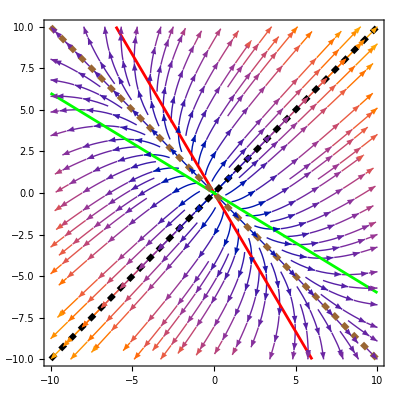

```mathematica
Show[(*1. The Vector Field*)StreamPlot[{5/4x+3/4 y,3/4x+5/4y},{x,-10,10},{y,-10,10}],(*2. The Nullclines*)ContourPlot[{5/4x+3/4 y==0,3/4x+5/4y==0},{x,-10,10},{y,-10,10},ContourStyle->{Red,Green}],(*3. The Eigendirection*)Plot[{x,- x},{x,-10,10},PlotStyle->{{Black,Dashed,AbsoluteThickness[4]},{Brown,Dashed,AbsoluteThickness[4]}}]]
```

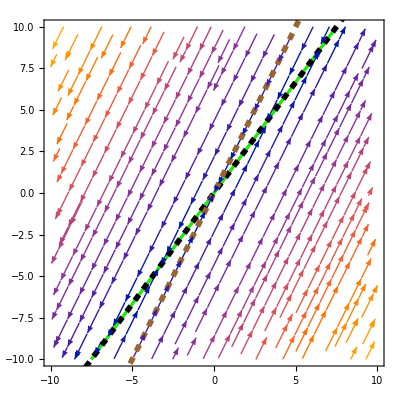

```mathematica
Show[(*1. The Vector Field*)StreamPlot[{4 x-3 y,8 x-6 y},{x,-10,10},{y,-10,10}],(*2. The Overlapping Nullclines*)ContourPlot[{4 x-3 y==0,8 x-6 y==0},{x,-10,10},{y,-10,10},ContourStyle->{Red,Green}],(*3. The Eigendirections with extra thickness*)Plot[{(4/3) x,2 x},{x,-10,10},PlotStyle->{{Black,Dashed,AbsoluteThickness[4]},{Brown,Dashed,AbsoluteThickness[4]}}]]
```

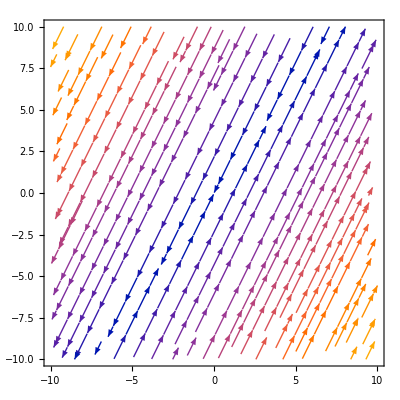

```mathematica
StreamPlot[{4 x-3 y,8 x-6 y},{x,-10,10},{y,-10,10}]
```

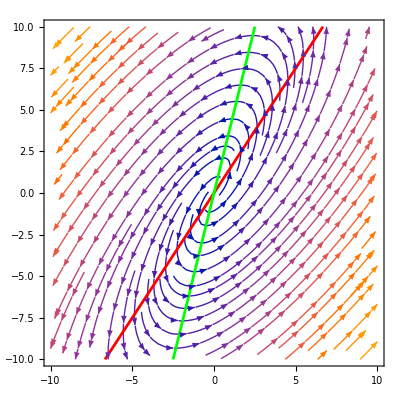

```mathematica
Show[(*1. The Vector Field*)StreamPlot[{3x-2 y,4 x-1 y},{x,-10,10},{y,-10,10}],(*2. The Overlapping Nullclines*)ContourPlot[{3x-2 y==0,4 x-1 y==0},{x,-10,10},{y,-10,10},ContourStyle->{Red,Green}]](*3. The Eigendirections with extra thickness*)
```

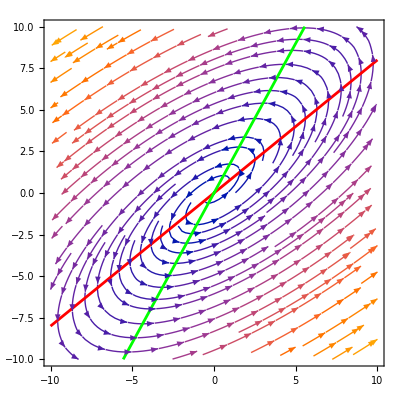

```mathematica
Show[(*1. The Vector Field*)StreamPlot[{2x-5/2 y,9/5 x-1 y},{x,-10,10},{y,-10,10}],(*2. The Overlapping Nullclines*)ContourPlot[{2x-5/2y==0,9/5x-1 y==0},{x,-10,10},{y,-10,10},ContourStyle->{Red,Green}]](*3. The Eigendirections with extra thickness*)
```